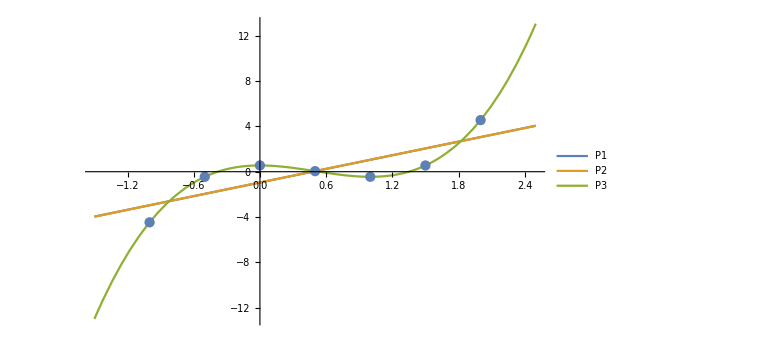

plot.png

```mathematica
L1[x_]:=-0.954464285714+2.004357142857 x^1

L2[x_]:=-0.951642857143+2.008119047619 x^1+-0.003761904762 x^2

L3[x_]:=0.551023809524+0.004563492063 x^1+-3.009095238095 x^2+2.003555555556 x^3
p1 = Plot[{L1[x],L2[x],L3[x]},{x,-1.5,2.5},PlotLegends->{"P1","P2","P3"},ImageSize->Large ];
f = {-4.467,-0.452,0.551,0.048,-0.447,0.549,4.552};
z = {-1.0,-0.5,0.0,0.5,1.0,1.5,2.0};
p2 = ListPlot[Transpose[{z,f}],ImageSize->Large];
Show[p1,p2]
Export["plot.png",Show[p1,p2]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["plot.png"]]]
```